Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

1 - 10 Find the path and sketch it.

1.  z[t_]=(1+ⅈ/2)t  , 2≤t≤5

For the first plot at least, this can be handled by treating ⅈ as equal to 1, and labeling the axes appropriately.

```mathematica
Clear["Global`*"]
```

```mathematica
z[t_]=(1+ⅈ/2)t
```

(1+ⅈ/2) t

```mathematica
p1=Plot[{Re[z[t]],Im[z[t]]},{t,2,5},PlotStyle->{Blue,Red},AxesLabel->{"Re","Blue,real;Red,imag;Brown,cmplx"},ImageSize->250,PlotRange->{0,8},GridLines->Automatic];
```

```mathematica
p2=Plot[t+t/2,{t,2,5},PlotStyle->{Brown},AxesLabel->Automatic,ImageSize->250];
```

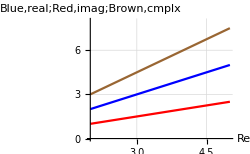

```mathematica
Show[p1,p2]
```

3. z[t_]=t+2 ⅈ t^2 , 1≤t≤2

The Plot function is very limited, but seems to handle the first two problems.

```mathematica
Clear["Global`*"]
```

```mathematica
z[t_]=t+2 ⅈ t^2
```

t+2 ⅈ t^2

```mathematica
p1=Plot[{Re[z[t]],Im[z[t]]},{t,1,2},PlotStyle->{Blue,Red},AxesLabel->{"Re","Blue,real;Red,imag;Brown,cmplx"},ImageSize->300,PlotRange->Full,GridLines->Automatic];
```

```mathematica
p2=Plot[t+2 t^2,{t,1,2},PlotStyle->{Brown},AxesLabel->Automatic,ImageSize->300];
```

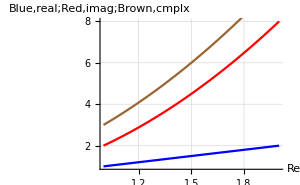

```mathematica
Show[p1,p2]
```

5.  z[t_]=3-ⅈ+√10 ⅇ^-ⅈt  , 0≤t≤2 π

```mathematica
Clear["Global`*"]
```

```mathematica
z[t_]=3-ⅈ+√10 ⅇ^(-ⅈ t)
```

(3-ⅈ)+√10 ⅇ^(-ⅈ t)

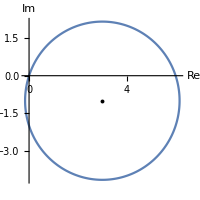

```mathematica
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,2π},ImageSize->200,Epilog->{PointSize[0.014],Point[{3,-1}]},AxesLabel->{"Re","Im"}]
```

The radius is √10, and √(3^2+1^2)=10, so the circle goes through the origin. Watching the result of increasing t from π/2to π reveals in which direction the function develops. The function is oriented clockwise.

7.  z[t_]=2+4 ⅇ^(π ⅈ t/2)  , 0≤t≤2

```mathematica
Clear["Global`*"]
```

```mathematica
z[t_]=2+4 ⅇ^(π ⅈ t/2)
```

2+4 ⅇ^((ⅈ π t)/2)

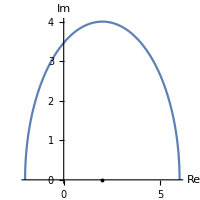

```mathematica
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,2},ImageSize->200,Epilog->{PointSize[0.014],Point[{2,0}]},AxesLabel->{"Re","Im"}]
```

Increasing t from 1 to 2 shows that the function is oriented counterclockwise.

9.  z[t_]=t+ⅈ t^3 , -2≤t≤2

```mathematica
Clear["Global`*"]
```

```mathematica
z[t_]=t+ⅈ t^3
```

t+ⅈ t^3

```mathematica
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,-2,2},ImageSize->100,Epilog->{PointSize[0.014],Point[{2,0}]},AxesLabel->{"Re","Im"}]
```

-Graphics-

Increasing t-max from 0 to 2 shows that the function is oriented from lower left to upper right.

11 - 20 Find a parametric representation

11.  Segment from (-1, 1) to (1, 3)

This one turns out to be just finding the equation of a line.

```mathematica
Clear["Global`*"]
```

```mathematica
p1=ListPlot[{{-1,1},{1,3}},ImageSize->110, AspectRatio->1.33,PlotMarkers->{Automatic,Small}];
p2=Plot[x+2,{x,-1,3},ImageSize->110];
Show[p1,p2]
```

-Graphics-

The nuts and bolts of the equation calculation.

```mathematica
m=(3-1)/(1-(-1))
```

1

```mathematica
as=y-Subscript[y, 1]==m(x-Subscript[x, 1])
```

y-y_1==x-x_1

```mathematica
as1=as/.{Subscript[x, 1]->1,Subscript[y, 1]->3}
```

-3+y==-1+x

```mathematica
Solve[as1,{y}]
```

{{y→2+x}}

```mathematica
ap=x+y ⅈ/.y->2+x
```

x+ⅈ (2+x)

```mathematica
ap1=ap/.x->t
```

t+ⅈ (2+t)

This expresses the equation of the line in parametric terms.

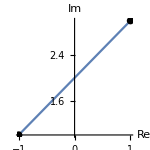

```mathematica
ParametricPlot[{Re[t+ⅈ (2+t)],Im[t+ⅈ (2+t)]},{t,-1,1},ImageSize->150,Epilog->{PointSize[0.035],Point[{{-1,1},{1,3}}]},AxesLabel->{"Re","Im"}]
```

13. Upper half of Abs[z - 2 + I] == 2 from (4, -1) to (0, -1)

The first thing I have to understand are the points given, (4,-1), (0,-1). From the other given expressions I have to think these are points in the complex plane. When it says “upper half” it makes me think it is a circle.

On the site at https://mathhelpboards.com/analysis-50/equation-circle-complex-plane-6771.html I found the following

Let z=x+ⅈ y, a=s+ⅈ t
Then the equation of the circle can be written as
|z-a|=r  (a=center, r=radius)
(x-s)^2+(y-t)^2=r^2
x^2+y^2-2 x s-2 y t+t^2+s^2=r^2
Although the gist of the above lines seems to be to get back to ℝ completely, some of the expressions can be used in the present ℂ case.

```mathematica
Clear["Global`*"]
```

```mathematica
z[t_]=Abs[z-(2-ⅈ)]==2
```

Abs[(-2+ⅈ)+z]==2

The center is already recognizable from the above, as is the radius, from the problem description.

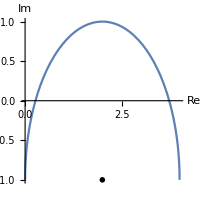

```mathematica
ParametricPlot[{2 Cos[t]+2,2 Sin[t]-1},{t,0,π},ImageSize->200,Epilog->{PointSize[0.02],Point[{{2,-1},{1,3}}]},AxesLabel->{"Re","Im"}]
```

Above: By trying the upper t boundary of π/2 before using π, I can see that the curve develops to the left and is therefore oriented counter-clockwise, as the problem description requires. Knowing the center and radius, it is only necessary to figure out how to express these in parametric plot parlance, which is easy. So there is a plot. However, the text answer is not yet achieved.

Below is shown another style of expressing the function z parametrically, closer to the text answer style.

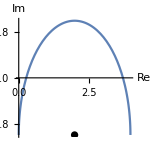

```mathematica
ParametricPlot[{Re[2-ⅈ+2(Cos[t]+ⅈ Sin[t])],Im[2-ⅈ+2(Cos[t]+ⅈ Sin[t])]},{t,0, π},ImageSize->150,Epilog->{PointSize[0.035],Point[{{2,-1},{1,3}}]},AxesLabel->{"Re","Im"}]
```

And below yet a further progression in style, this one close enough to get the green for text answer match.

```mathematica
ParametricPlot[{Re[2-ⅈ+2 ⅇ^(ⅈ t)],Im[2-ⅈ+2 ⅇ^(ⅈ t)]},{t,0, π},ImageSize->150,Epilog->{PointSize[0.035],Point[{{2,-1},{1,3}}]},AxesLabel->{"Re","Im"}]
```

-Graphics-

15.  x^2-4 y^2==4, the branch through (2,0)

From the form of the equation, it can be seen that a hyperbolic is being described.

```mathematica
ContourPlot[x^2/4-y^2==1,{x,-3,3},{y,-3,3},ImageSize->120]
```

-Graphics-

```mathematica
Solve[x^2/4-y^2==1,y]
```

{{y→-1/2 √(-4+x^2)},{y→1/2 √(-4+x^2)}}

Using blind parameterization with x -> t

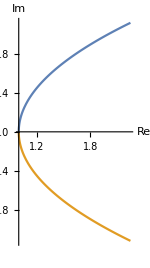

```mathematica
pduo=ParametricPlot[{{Re[t^2/4+1/2 √(-4+t^2)ⅈ],Im[t^2/4+1/2 √(-4+t^2)ⅈ]},{Re[t^2/4-1/2 √(-4+t^2)ⅈ],Im[t^2/4-1/2 √(-4+t^2)ⅈ]}},{t,2, 3},ImageSize->150,AxesLabel->{"Re","Im"}]
```

The domain of t was determined by trial and error. It can’t be less than 2, and must extend somewhat to the right of 2.

17.  Abs[z + a + I b] == r, clockwise

This is a circle, expressible as

```mathematica
HoldForm[Abs[z-(-a-ⅈ b)]==r]
```

Abs[z-(-a-ⅈ b)]==r

The radius is r, and the center is the point (-a,-b). To make a plot,

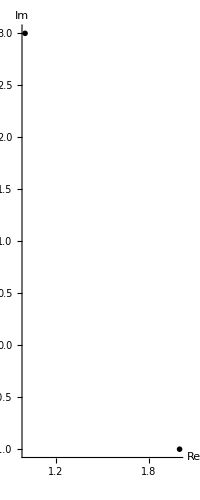

```mathematica
deco=ParametricPlot[{r Cos[t]+a,r Sin[t]-b},{t,0,2π},ImageSize->200,Epilog->{PointSize[0.02],Point[{{2,-1},{1,3}}]},AxesLabel->{"Re","Im"}]
```

Taking a green ribbon for an empty plot! To get the plot to show something, make substitutions, as using {-1,-1} for {-a,-b} and 1.5 for r.

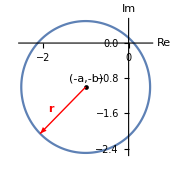

```mathematica
deco1=ParametricPlot[{1.5 Cos[t]-1,1.5 Sin[t]-1},{t,0,2π},ImageSize->170,Epilog->{{PointSize[0.02],Point[{-1,-1}]},{Text["(-a,-b)",{-1,-0.8}]},{Text[Style["r",Bold,Red,Medium],{-1.8,-1.5}]},{Red,Arrowheads[.05],Arrow[{{-1,-1},{-1-1.5Cos[π/4],-1-1.5Cos[π/4]}}]}},AxesLabel->{"Re","Im"}]
```

19.Parabola y==1-1/4 x^2  (-2≤x≤2)

```mathematica
Clear["Global`*"]
```

In the first step of parameterization, let x = t

```mathematica
y==1-1/4 x^2
```

y==1-x^2/4

```mathematica
y==1-t^2/4
```

y==1-t^2/4

Now check the boundary values of y,

```mathematica
y==1-t^2/4/.t->-2
```

y==0

```mathematica
y==1-t^2/4/.t->2
```

y==0

The boundary values have no effect on the value of y, so

```mathematica
z[t_]=x[t]+ⅈ y[t]
```

x[t]+ⅈ y[t]

```mathematica
z[t_]=t +ⅈ (1-1/4 t^2)
```

t+ⅈ (1-t^2/4)

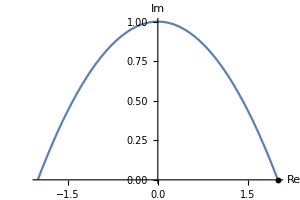

```mathematica
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,-2,2},ImageSize->300,Epilog->{PointSize[0.014],Point[{2,0}]},AxesLabel->{"Re","Im"}]
```

21 - 30 Integration
Integrate by the first method or state why it does not apply and use the second method.

21.  ∫_C Re[z]ⅆz  , the shortest path from 1+ⅈ to 3+ⅈ

I guess I should find the shortest distance between these two points. For points (a,b) and (s,t) the distance is

d=√((s-a)^2+(t-b)^2)

```mathematica
d1=√((1-3)^2+(1-1)^2)
```

2

or

```mathematica
d2=√((3-1)^2+(1-1)^2)
```

2

This distance calculation is just an aside, I believe.

```mathematica
Clear["Global`*"]
```

```mathematica
∫_(1+ⅈ)^(3+ⅈ) zⅆz
```

4+2 ⅈ

The answer in yellow does not match the text answer. In the general case of such complex integrations, it appears that Mathematica prefers not to see the region of application.  However, since the answer is questionable, I can try separation:

```mathematica
∫_(1+ⅈ)^(3+ⅈ) Re[z]ⅆz
```

4

```mathematica
∫_(1+ⅈ)^(3+ⅈ) Im[z]ⅆz
```

2

Done separately, the Mathematica answer is found. However, see below, as numbered line (9) does not say to do the parts separately. First, a couple of plots can’t hurt.

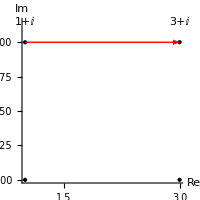

```mathematica
Graphics[{{Point[{1,0}]},{Point[{3,0}]},{Point[{1,1}]},{Point[{3,1}]},{Red,Arrowheads[.07],Arrow[{{1,1},{3,1}}]},{Text["3+ⅈ",{3.0,1.15}]},{Text["1+ⅈ",{1,1.15}]}},Axes->True, ImageSize->200,AxesLabel->{"Re","Im"}]
```

```mathematica
Plot[x^2/2,{x,1,3},ImageSize->125]
```

-Graphics-

Discussion of the discrepancy. Numbered line (9) on p. 647, I think, tends to support Mathematica. The burden of numbered line (9) seems to be that, for analytic functions, the z form can be retained during the integration. This would therefore seem to evaluate as

```mathematica
(3+ⅈ)^2 (*top evaluation*)
```

8+6 ⅈ

```mathematica
(1+ⅈ)^2(*bottom evaluation*)
```

2 ⅈ

```mathematica
1/2(8+4ⅈ)(*applying integration factor to difference between top and bottom*)
```

4+2 ⅈ

in agreement with Mathematica's answer (but not that of the text).

23. ∫_C e^z ⅆz , C, the shortest path from πⅈ to 2π ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
∫_(π ⅈ)^(2 π ⅈ) ⅇ^z ⅆz
```

2

25. ∫_C z Exp[z^2]ⅆz , C from 1 along the axes to ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
∫_1^ⅈ z ⅇ^(z^2)ⅆz
```

-(-1+ⅇ^2)/(2 ⅇ)

```mathematica
TrigToExp[-Sinh[1]]
```

1/(2 ⅇ)-ⅇ/2

```mathematica
Together[1/(2 ⅇ)-ⅇ/2]
```

(1-ⅇ^2)/(2 ⅇ)

The green cell above is equivalent to the text answer, as shown by the yellow cells above.

27. ∫_C Sec[z]^2 ⅆz , any path from π/4 to (π ⅈ)/4

```mathematica
Clear["Global`*"]
```

```mathematica
∫_(π/4)^(π/4 ⅈ) Sec[z]^2 ⅆz
```

-1+ⅈ Tanh[π/4]

The green cell above matches the text answer.

29. ∫_C Im[z^2]ⅆz , counterclockwise around the triangle with vertices 0,1,ⅈ

```mathematica
Clear["Global`*"]
```

```mathematica
eq1=∫_0^1 Im[z^2]ⅆz
```

0

```mathematica
eq2=∫_1^ⅈ z^2 ⅆz
```

-1/3-ⅈ/3

```mathematica
eq3=Together[eq1+eq2]
```

-1/3-ⅈ/3

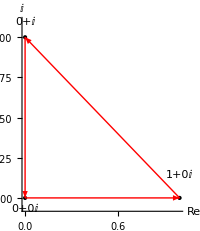

```mathematica
Graphics[{{Point[{1,0}]},{Point[{0,0}]},{Point[{0,1}]},{Red,Arrowheads[.07],Arrow[{{1,0},{0,1}}]},{Red,Arrowheads[.07],Arrow[{{0,1},{0,0}}]},{Text["1+0ⅈ",{1.0,0.15}]},{Text["0+0ⅈ",{0,-0.06}]},{Red,Arrowheads[.07],Arrow[{{0,0},{1,0}}]},{Text["0+ⅈ",{0,1.1}]}},Axes->True, ImageSize->200,AxesLabel->{"Re","ⅈ"}]
```

The green cell above matches the text answer, except I cannot by any means get the terms to merge. The arrows show the counter-clockwise sense.

The fact that Mathematica came through with the text answer on 23, 25, 27, and 29 helps build confidence about no. 21.